## Load MathQ - beta

```mathematica
SetDirectory[NotebookDirectory[]];

nb=CreateDocument[Get["MathQ-beta.nb"], WindowSelected->False];
NotebookEvaluate@nb;
NotebookClose[nb];
```

## Lesson 1 - Building a Lattice

### Basic lattices

#### Built-in lattice presets

We have a number of basic lattice presets (in 1D, 2D and 3D), and some more elaborate lattice models (we will not discuss these)

```mathematica
LatticePresets
```

{BCC,Cubic,FCC,Honeycomb,Linear,Square,Triangular,TwistedHoneycombBilayer,TwistedHoneycombBilayer,HoneycombNanoribbon}

```mathematica
lat = BuildLattice["Honeycomb"]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

```mathematica
List@@lat
```

{Sites→{{{0.,-0.288675}},{{0.,0.288675}}},Tags→{A,B},BravaisVectors→{{0.5,0.866025},{-0.5,0.866025}},EmbeddingDimensions→2}

```mathematica
lat["Sites"]
```

{{{0.,-0.288675}},{{0.,0.288675}}}

```mathematica
lat["Tags"]
```

{A,B}

```mathematica
lat["LatticeDimensions"]
```

2

```mathematica
lat["BravaisVectors"]
```

{{0.5,0.866025},{-0.5,0.866025}}

A useful command is PlotLattice. By default it plots the unitcell and (in dimmer color) the neighboring cells along the Bravais vectors (a1, a2, and a1+a2 here).
Note that PlotLattice accepts any option from Graphics (see Options[PlotLattice] for complete list)

```mathematica
PlotLattice[lat]
PlotLattice[lat, Axes->True,Frame->True,BaseStyle->FontSize->15]
```

PlotLattice[BuildLattice[Honeycomb]]

PlotLattice[BuildLattice[Honeycomb],Axes→True,Frame→True,BaseStyle→FontSize→15]

We can also choose to plot more (or less) unit cells

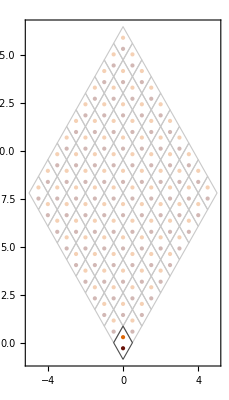

```mathematica
PlotLattice[lat, UnitCells->10, Axes->True, Frame->True,BaseStyle->FontSize->15, BoxCenterAtOrigin->True]
```

The lattice constant is always 1 in the built-in presets. We can change that (in any lattice) like this

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

{{1.,1.73205},{-1.,1.73205}}

{2.,2.}

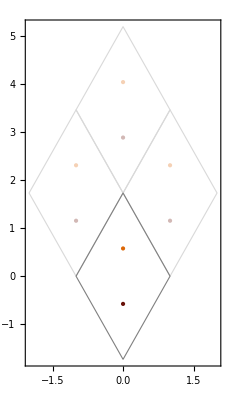

```mathematica
lat=BuildLattice["Honeycomb",LatticeConstant->2]
lat["BravaisVectors"]
Norm/@%
PlotLattice[lat, Axes->True,Axes->True, Frame->True,BaseStyle->FontSize->15]
```

#### Custom lattices

We can provide arbitrary bravais vectors and basis sites for any lattice

```mathematica
With[{
bravais={{1,0,0},{0,1,0},{0,0,1}}, sublats = {"A"->{{0,0,0}},"B"->{{0,.5,0},{.6,0,.6}}}},
lat = BuildLattice[{bravais,sublats}]
]
```

MQLattice[<NumberOfSites=3, LatticeDimensions=3, EmbeddingDimensions=3>]

```mathematica
PlotLattice[lat, Axes->True, Boxed->True]
```

-Graphics3D-

```mathematica
PlotLattice[lat, Axes->True, Boxed->True, Labels->"Numbers"]
```

-Graphics3D-

```mathematica
PlotLattice[lat, Axes->True, Boxed->True, Labels->"Tags"]
```

-Graphics3D-

### Derived lattices

#### Superlattices

```mathematica
lat = BuildLattice["Square"]
```

MQLattice[<NumberOfSites=1, LatticeDimensions=2, EmbeddingDimensions=2>]

A supercell that is 10 times larger in all directions

```mathematica
lat2=BuildLattice[lat, Supercell->10]
```

MQLattice[<NumberOfSites=100, LatticeDimensions=2, EmbeddingDimensions=2>]

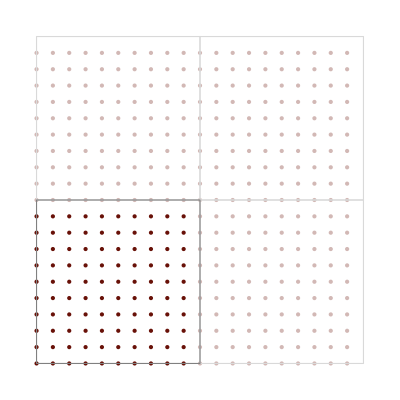

```mathematica
PlotLattice[lat2]
```

A supercell that is 3 times larger along the first bravais vector, and 5 times larger along the second

```mathematica
lat3=BuildLattice[lat, Supercell->{3,5}]
```

MQLattice[<NumberOfSites=15, LatticeDimensions=2, EmbeddingDimensions=2>]

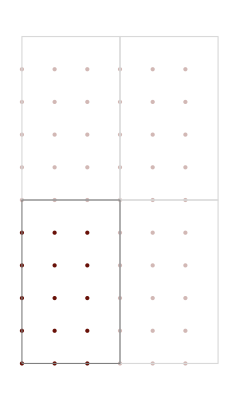

```mathematica
PlotLattice[lat3]
```

A supercell that is generated by a1’ = 4a1 - 4a2 and a2’ = 5a2

```mathematica
lat4=BuildLattice[lat, Supercell->{{4,-4},{0,5}}]
```

MQLattice[<NumberOfSites=20, LatticeDimensions=2, EmbeddingDimensions=2>]

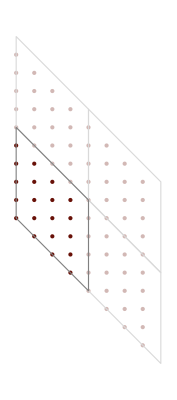

```mathematica
PlotLattice[lat4]
```

We can also do it in one go

```mathematica
PlotLattice[BuildLattice["Square", Supercell->{{4,-4},{0,5}}]]
```

-Graphics-

#### Regions

```mathematica
lat = BuildLattice["Square"]
```

MQLattice[<NumberOfSites=1, LatticeDimensions=2, EmbeddingDimensions=2>]

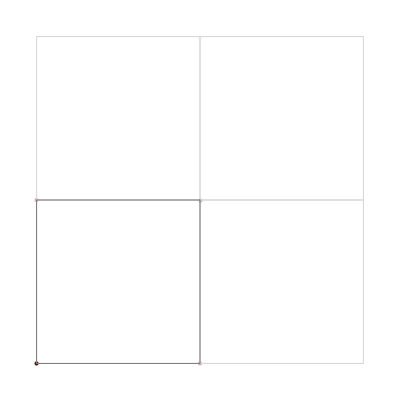

```mathematica
PlotLattice[lat]
```

Note: We may draw cells boxes with their center (instead of their vertex) at the origin. We can also specify a line style

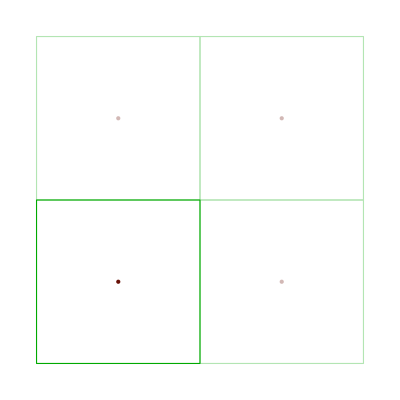

```mathematica
PlotLattice[lat, BoxCenterAtOrigin->True, CellBoxStyle->Darker[Green]]
```

We now wish to “fill” a bounded region with this periodic lattice. The result is a non-periodic (bounded) lattice

MQLattice[<NumberOfSites=2809, LatticeDimensions=0, EmbeddingDimensions=2>]

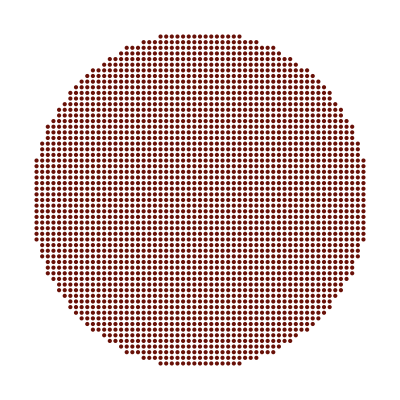

```mathematica
myregion=Function[{r},Norm[r]<30];
lat2=BuildLattice[lat, Bounded->{Region->myregion}]
PlotLattice[lat2]
```

A more complicated example

```mathematica
lat = BuildLattice["BCC", Supercell->{3,1,1}]
```

MQLattice[<NumberOfSites=3, LatticeDimensions=3, EmbeddingDimensions=3>]

```mathematica
PlotLattice[lat, UnitCells->5]
```

-Graphics3D-

Note: In 3D we can render a “pretty” lattice using a finite SiteRadius (caution: unstable for large lattices)

```mathematica
PlotLattice[lat, UnitCells->5, SiteRadius->.4, BoxedCells->None]
```

-Graphics3D-

We will make lat bounded along two axes (second and third), leaving the first one unbounded

```mathematica
myregion = Function[{r},Norm[r[[2;;3]]]<8];
lat2=BuildLattice[lat, Bounded->{Axes->{2,3}, Region->myregion}]
PlotLattice[lat2, Boxed->True,SiteRadius->.4]
```

MQLattice[<NumberOfSites=1203, LatticeDimensions=1, EmbeddingDimensions=3>]

-Graphics3D-

#### Reshaping unit cells

```mathematica
myregion = Function[{r},Norm[r[[2;;3]]]<8];
lat2=BuildLattice["BCC", Supercell->{4,1,1},Bounded->{Axes->{2,3}, Region->myregion}]
PlotLattice[lat2, Boxed->True,SiteRadius->.4]
```

MQLattice[<NumberOfSites=1604, LatticeDimensions=1, EmbeddingDimensions=3>]

-Graphics3D-

We can choose the unit cell of a periodic lattice in many ways that generate, upon translation along the bravais vectors, the same sublattice. We can thus “reshape” the unit cell freely to our preferred shape.

```mathematica
myregion=Function[{r},r[[1]]>0];
lat3=BuildLattice[lat2,Reshape->{Axis->1,Region->myregion}]
PlotLattice[lat3,Boxed->True,SiteRadius->.4]
```

MQLattice[<NumberOfSites=1203, LatticeDimensions=1, EmbeddingDimensions=3>]

-Graphics3D-

#### Deforming lattices

```mathematica
myregion=Function[{r},Norm[r]<10];
lat=BuildLattice["Honeycomb",EmbeddingDimensions->3,Bounded->{Region->myregion}]
PlotLattice[lat, Boxed->True,SiteRadius->.3, SiteColors->{White,Darker[Green]}, Axes->True]
```

MQLattice[<NumberOfSites=726, LatticeDimensions=0, EmbeddingDimensions=3>]

-Graphics3D-

```mathematica
mydeformation=Function[{r},r+4Exp[-Norm[r]^2/(2*3^2)]{0,0,1}];
lat2=BuildLattice[lat, Transform->mydeformation]
PlotLattice[lat2, SiteRadius->.3,SiteColors->{White, Darker[Green]}, Boxed->True]
```

MQLattice[<NumberOfSites=726, LatticeDimensions=0, EmbeddingDimensions=3>]

-Graphics3D-

We can pass the site tag as a second argument to spatial functions

```mathematica
mydeformation=Function[{r, tag},r+4Exp[-Norm[r]^2/(2*3^2)]{0,0,1}If[tag=="A",1,-1]];
lat2=BuildLattice[lat, Transform->mydeformation]
PlotLattice[lat2, SiteRadius->.3,SiteColors->{White, Darker[Green]}, Boxed->True]
```

MQLattice[<NumberOfSites=726, LatticeDimensions=0, EmbeddingDimensions=3>]

-Graphics3D-

Deformations of periodic lattices are applied only to the base unit cell, and are therefore extended periodically

```mathematica
lat=BuildLattice["Honeycomb",EmbeddingDimensions->3,Supercell->20]
mydeformation=Function[{r},r+4Exp[-Norm[r-{0,20(√3)/2,0}]^2/(2*3^2)]{0,0,1}];
lat2=BuildLattice[lat, Transform->mydeformation]
PlotLattice[lat2, SiteRadius->.3,SiteColors->{White, Darker[Green]}, BoxedCells->False]
```

MQLattice[<NumberOfSites=800, LatticeDimensions=2, EmbeddingDimensions=3>]

MQLattice[<NumberOfSites=800, LatticeDimensions=2, EmbeddingDimensions=3>]

-Graphics3D-

#### Combining lattices

```mathematica
botlat=BuildLattice["Honeycomb",EmbeddingDimensions->3,Tags->{"Ab", "Bb"},
Bounded->{Region->Function[{r},Norm[r]<15]}, 
Transform->Function[{r}, r-{0,0,.5}]]
toplat=BuildLattice["Honeycomb",EmbeddingDimensions->3,Tags->{"At", "Bt"},
Bounded->{Region->Function[{r},Norm[r]<15]}, 
Transform->Function[{r}, ({{Cos[.2], -Sin[.2], 0}, {Sin[.2], Cos[.2], 0}, {0, 0, 1}}).r+{0,0,.5}]]
PlotLattice[{botlat,toplat},SiteRadius->.2, SiteColors->{{Black,Gray},{Purple,White}}, ViewPoint->Top]
PlotLattice[{botlat,toplat},SiteRadius->.2, SiteColors->{{Black,Gray},{Purple,White}}, ViewPoint->Front]
```

MQLattice[<NumberOfSites=1630, LatticeDimensions=0, EmbeddingDimensions=3>]

MQLattice[<NumberOfSites=1630, LatticeDimensions=0, EmbeddingDimensions=3>]

-Graphics3D-

-Graphics3D-

Lattices can be combined into one if they have the same periodicity (same Bravais vectors - none in the example above)

```mathematica
lat=CombineLattices[botlat, toplat]
PlotLattice[lat,SiteRadius->.2, ViewPoint->Top]
```

MQLattice[<NumberOfSites=3260, LatticeDimensions=0, EmbeddingDimensions=3>]

-Graphics3D-

An example with shared periodicity

MQLattice[<NumberOfSites=16, LatticeDimensions=2, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=4, LatticeDimensions=2, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=20, LatticeDimensions=2, EmbeddingDimensions=2>]

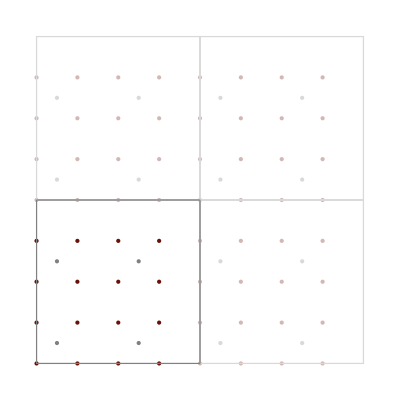

{{4.,0.},{0.,4.}}

{{4.,0.},{0.,4.}}

```mathematica
lat1=BuildLattice["Square",Supercell->4]
lat2=BuildLattice["Square",Supercell->2, Transform->Function[{r},2r+{1/2,1/2}]]
lat3=CombineLattices[lat1,lat2]

PlotLattice[{lat1,lat2}]
lat1["BravaisVectors"]
lat2["BravaisVectors"]
```

MQLattice[<NumberOfSites=20, LatticeDimensions=2, EmbeddingDimensions=2>]

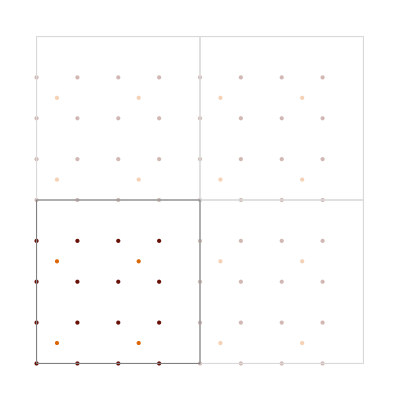

```mathematica
lat3=CombineLattices[lat1,lat2]
PlotLattice[lat3]
```

Attempting to combine lattices with different Bravais vectors throws an “Incompatible lattices” error

```mathematica
lat1=BuildLattice["Square",Supercell->4]
lat2=BuildLattice["Square",Supercell->2]
lat1["BravaisVectors"]
lat2["BravaisVectors"]
lat3=CombineLattices[lat1,lat2]
```

MQLattice[<NumberOfSites=16, LatticeDimensions=2, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=4, LatticeDimensions=2, EmbeddingDimensions=2>]

{{4.,0.},{0.,4.}}

{{2.,0.},{0.,2.}}

CombineLattices::bravais: Lattices are not compatible, since their Bravais vectors are not the same.

$Aborted

## Lesson 2 - Building a System

### One orbital per site

#### Non-periodic lattice

```mathematica
lat = BuildLattice["Square", Bounded->{Region->Function[{r},Norm[r]<5]}]
sys =BuildSystem[lat,
HoppingRange->1,
Onsite->Function[{r},2],
Hopping->Function[{r1, r2},1]]
```

MQLattice[<NumberOfSites=69, LatticeDimensions=0, EmbeddingDimensions=2>]

MQSystem[<NumberOfSites=69, SiteDimensions=1, LatticeDimensions=0>]

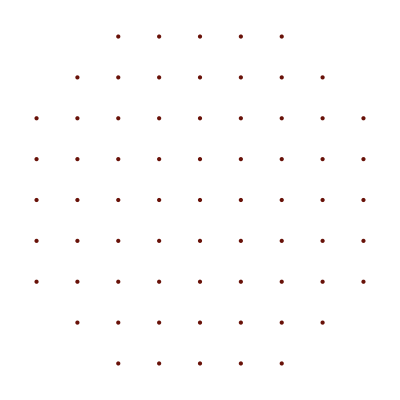

```mathematica
PlotLattice[lat]
```

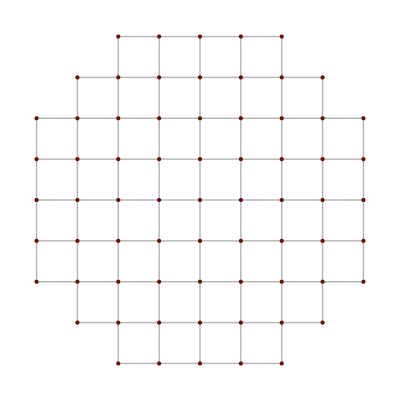

```mathematica
PlotLattice[sys]
```

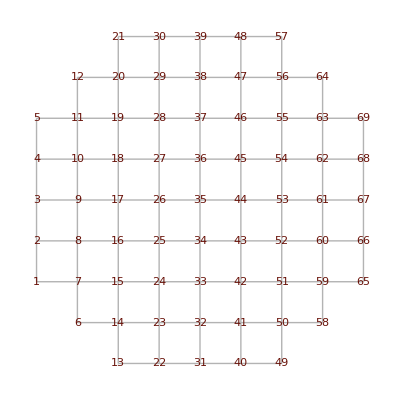

```mathematica
PlotLattice[sys,Labels->"Numbers", SiteTooltips->True, LinkTooltips->True]
```

To access the Hamiltonian matrix use sys[“H”]

```mathematica
sys["H"]
```

SparseArray[<309>, {69, 69}]

```mathematica
MatrixForm[sys["H"]]
```

(2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2)

```mathematica
sys["H"][[23,23]]
sys["H"][[23,24]]
```

2

1

#### Periodic lattice

```mathematica
lat = BuildLattice["Linear", Supercell->3]
sys =BuildSystem[lat,
HoppingRange->1,
Onsite->Function[{r},2],
Hopping->Function[{r1, r2},-1]]
```

MQLattice[<NumberOfSites=3, LatticeDimensions=1, EmbeddingDimensions=1>]

MQSystem[<NumberOfSites=3, SiteDimensions=1, LatticeDimensions=1>]

```mathematica
PlotLattice[lat]
```

-Graphics-

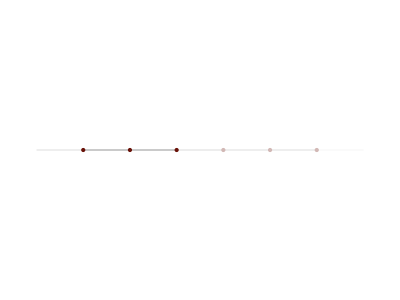

```mathematica
PlotLattice[sys, BoxedCells->False]
```

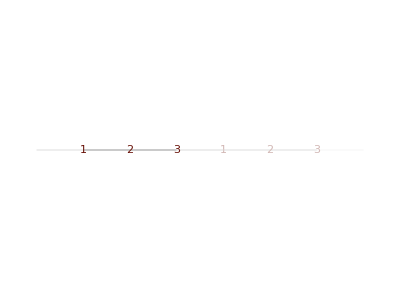

```mathematica
PlotLattice[sys,Labels->"Numbers", SiteTooltips->True, LinkTooltips->True]
```

sys[“H”] in this case gives the intra-unitcell Hamiltonian

```mathematica
MatrixForm[sys["H"]]
```

(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2)

sys[“HBloch”] gives also the inter-unitcell Hamiltonians

```mathematica
sys["HBloch"]
```

{{0}→SparseArray[<7>, {3, 3}],{-1}→SparseArray[<1>, {3, 3}],{1}→SparseArray[<1>, {3, 3}]}

```mathematica
MatrixForm/@sys["HBloch"][[All,2]]
```

{(2 | -1 | 0
-1 | 2 | -1
0 | -1 | 2),(0 | 0 | 0
0 | 0 | 0
-1 | 0 | 0),(0 | 0 | -1
0 | 0 | 0
0 | 0 | 0)}

```mathematica
{1}/.sys["HBloch"]
%[[1,3]]
```

SparseArray[<1>, {3, 3}]

-1

Limitation: a unit cell can only have hoppings to nearest-neighbor unit cells (including diagonals). If longer range hopping is required, just enlarge the unitcell with Supercell.

### Several orbitals per site

We just have to use a matrix Onsite and Hopping functions

```mathematica
lat = BuildLattice["Linear", Supercell->3]
sys =BuildSystem[lat,
HoppingRange->1,
Onsite->Function[{r},({{2, 0}, {0, 2}})],
Hopping->Function[{r1, r2},({{-1, 0}, {0, -1}})]]
```

MQLattice[<NumberOfSites=3, LatticeDimensions=1, EmbeddingDimensions=1>]

MQSystem[<NumberOfSites=3, SiteDimensions=2, LatticeDimensions=1>]

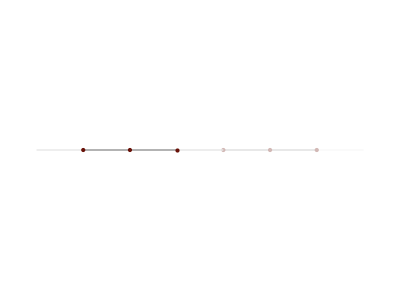

```mathematica
PlotLattice[sys, SiteTooltips->True, LinkTooltips->True]
```

```mathematica
MatrixForm[sys["H"]]
MatrixForm[sys["Flat"]["H"]]
```

((2 | 0
0 | 2) | (-1 | 0
0 | -1) | (0 | 0
0 | 0)
(-1 | 0
0 | -1) | (2 | 0
0 | 2) | (-1 | 0
0 | -1)
(0 | 0
0 | 0) | (-1 | 0
0 | -1) | (2 | 0
0 | 2))

(2 | 0 | -1 | 0 | 0 | 0
0 | 2 | 0 | -1 | 0 | 0
-1 | 0 | 2 | 0 | -1 | 0
0 | -1 | 0 | 2 | 0 | -1
0 | 0 | -1 | 0 | 2 | 0
0 | 0 | 0 | -1 | 0 | 2)

Example: Kane-Mele model (spin 1/2 per site)

```mathematica
lat = BuildLattice["Honeycomb", Tags->{"A","B"}]

With[{λ=0.1, t=3.16},KaneMele=Function[{r1,r2,tag1,tag2},If[Norm[r1-r2]≤1/√3,t({{1, 0}, {0, 1}}),ⅈ λ ({{1, 0}, {0, -1}})Cos[3ArcTan@@(r1-r2)]If[tag1==="A",1,-1]]]];
sys =BuildSystem[lat,HoppingRange->1,Onsite->Function[{r},({{0, 0}, {0, 0}})],Hopping->KaneMele]
```

MQLattice[<NumberOfSites=2, LatticeDimensions=2, EmbeddingDimensions=2>]

MQSystem[<NumberOfSites=2, SiteDimensions=2, LatticeDimensions=2>]

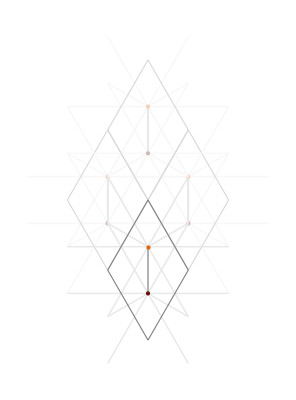

```mathematica
PlotLattice[sys, SiteTooltips->True, LinkTooltips->True, BoxCenterAtOrigin->True]
```

Example: BCS superconductor (Nambu representation H = (H_0 | Δ^+
Δ | -H_0^*) )

```mathematica
lat = BuildLattice["Cubic"]
With[{t=1, Δ=0.1, μ=0.4},
sys =BuildSystem[lat,HoppingRange->1,
Onsite->Function[{r},({{4t-μ, 0, 0, Δ}, {0, 4t-μ, -Δ, 0}, {0, -Δ, -(4t-μ), 0}, {Δ, 0, 0, -(4t-μ)}})],
Hopping->Function[{r1, r2},({{-t, 0, 0, 0}, {0, -t, 0, 0}, {0, 0, t, 0}, {0, 0, 0, t}})],
Nambu->True]
]
```

MQLattice[<NumberOfSites=1, LatticeDimensions=3, EmbeddingDimensions=3>]

MQSystem[<NumberOfSites=1, SiteDimensions=4, LatticeDimensions=3>]

```mathematica
PlotLattice[sys, SiteRadius->.3,LinkRadius->.08,SiteTooltips->True, LinkTooltips->True,BoxCenterAtOrigin->True]
```

-Graphics3D-

Limitation: currently, all sites should have the same “SiteDimensions” (number of orbitals per site). If they are different, one should add “dummy” decoupled orbitals

## Lesson 3 - Computing electronic structure

### Non-periodic systems

Let’s build a spinless px+ipy 2D superconductor model on a disk. But this time we make sys a function of a parameter (the gap)

```mathematica
diskregion=Function[{r},Norm[r]≤25];
lat = BuildLattice["Square",  Bounded->{Region->diskregion}]
k[r1_,r2_]=-ⅈ (r1-r2)/Norm[r1-r2]^2;
With[{t=1.0, μ=1.0},
pwavehoppingΔ[Δ_]=Function[{r1,r2},({{-t, 0}, {0, t}})+Δ({{0, k[r1,r2].{1,-ⅈ}}, {k[r1,r2].{1,ⅈ}, 0}})];
sysΔ[Δ_] =BuildSystem[lat,HoppingRange->1,Onsite->Function[{r},({{-μ, 0}, {0, μ}})],Hopping->pwavehoppingΔ[Δ]]];
```

MQLattice[<NumberOfSites=1961, LatticeDimensions=0, EmbeddingDimensions=2>]

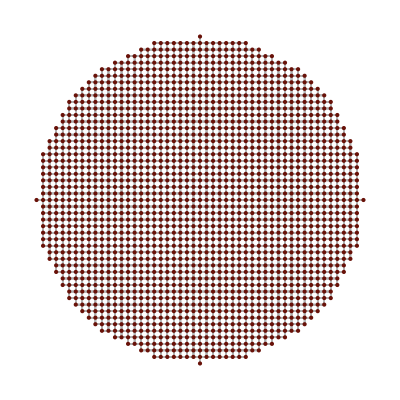

```mathematica
PlotLattice[sysΔ[.1]]
```

```mathematica
eigs0=Spectrum[sysΔ[0]];
eigs = Spectrum[sysΔ[0.1]];
```

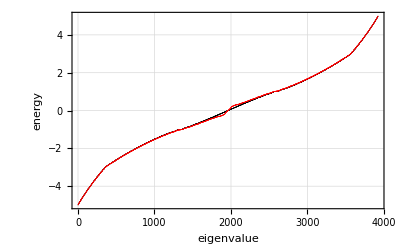

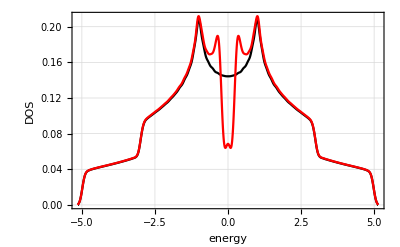

```mathematica
ListPlot[{eigs0, eigs},PlotStyle->{Black, Red}, PlotDefaults, FrameLabel->{"eigenvalue","energy"}, BaseStyle->PointSize[.001]]
SmoothHistogram[{eigs0, eigs},.07,PlotStyle->{Black, Red}, PlotDefaults, FrameLabel->{"energy","DOS"}]
```

```mathematica
eigs0=Spectrum[sysΔ[0], Levels->800];
eigs = Spectrum[sysΔ[0.5],Levels->800];
```

Eigenvalues::arh: Because finding 800 out of the 3922 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

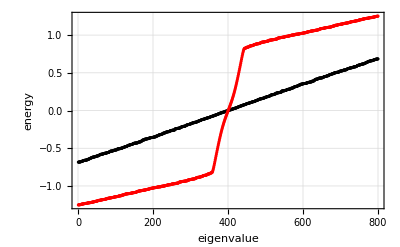

```mathematica
ListPlot[{eigs0, eigs}, PlotStyle->{Black, Red},PlotDefaults,FrameLabel->{"eigenvalue","energy"}]
```

Eigenstates can also be computed, preserving their site/orbital structure. The orbital structure can also be processed with the OrbitalFunction option.

```mathematica
Eigenstates[sysΔ[0.5],Levels->2]
Dimensions[%]
```

{{{0.0181086-0.0445603 ⅈ,-0.0438662-0.0178266 ⅈ},{-0.00457186-0.0770547 ⅈ,-0.0449023-0.0622825 ⅈ},{-0.00513852+0.0230652 ⅈ,0.0187613+0.0139894 ⅈ},1956,{-0.00457186-0.0770547 ⅈ,0.0449023+0.0622825 ⅈ},{0.0181086-0.0445603 ⅈ,0.0438662+0.0178266 ⅈ}},{1}}
 |  |  |  |

{2,1961,2}

```mathematica
Eigenstates[sysΔ[0.5],Levels->2, OrbitalFunction->Function[{ψ},Norm[ψ]^2]];
Dimensions[%]
```

{2,1961}

We may visualize eigenstates on the lattice

{0.173694,0.1868,0.200309,0.214164}

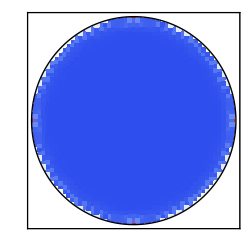
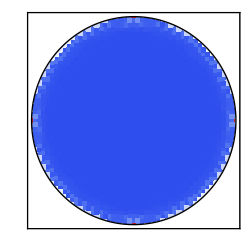
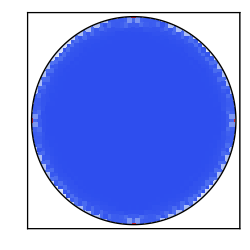
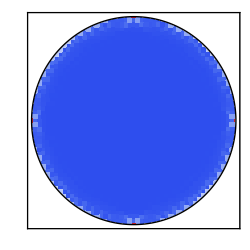

```mathematica
PlotEigenstates[sysΔ[0.5],EnergyOrigin->0.2,Levels->4,PrintEigenvalues->True,MaskRegion->diskregion]
```

{0.996406,0.99841,0.999306,1.0025}

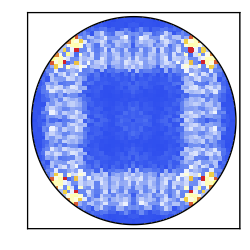
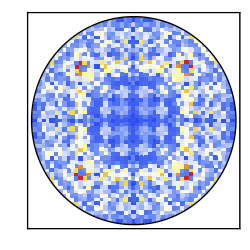
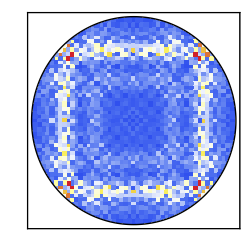
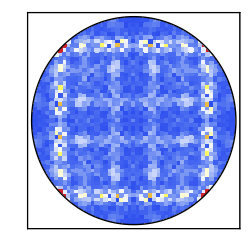

```mathematica
PlotEigenstates[sysΔ[0.5],EnergyOrigin->1.0,Levels->4,PrintEigenvalues->True, MaskRegion->diskregion]
```

We may also choose to plot a given function of the orbitals on each sites. For example, only the electron-like part of the wavefunction

{0.996406,0.99841,0.999306,1.0025}

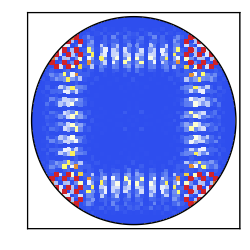
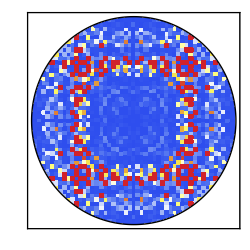
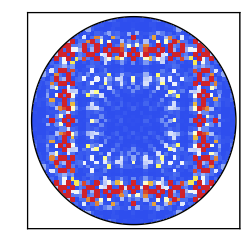
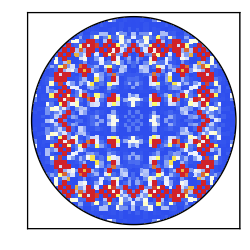

```mathematica
PlotEigenstates[sysΔ[0.5],EnergyOrigin->1.0,Levels->4,PrintEigenvalues->True,MaskRegion->diskregion, OrbitalFunction->Function[{ψ},Abs[ψ[[1]]]^2]]
```

A rather slow “BubblePlot” method is also available

{0.173694,0.1868,0.200309,0.214164}

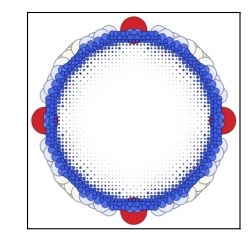
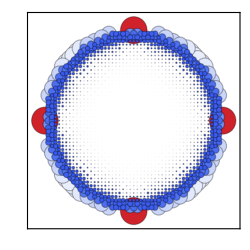
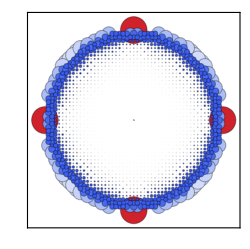
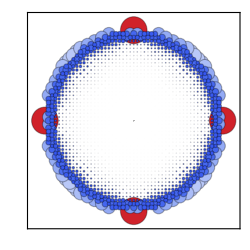

```mathematica
PlotEigenstates[sysΔ[0.5],EnergyOrigin->0.2,Levels->4,PrintEigenvalues->True,BubblePlot->True]
```

{0.996406,0.99841,0.999306,1.0025}

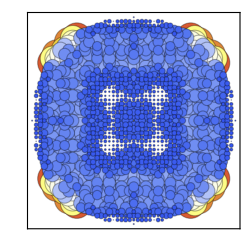
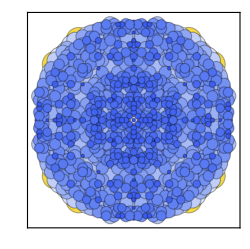
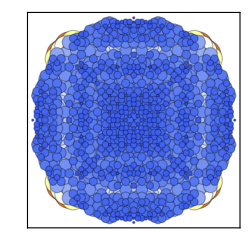
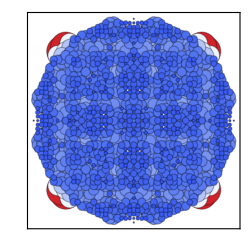

```mathematica
PlotEigenstates[sysΔ[0.5],EnergyOrigin->1.0,Levels->4,PrintEigenvalues->True,BubblePlot->True]
```

Kernel Polynomial Method for the DOS

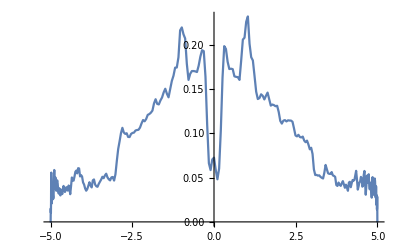

```mathematica
ListLinePlot[DOSKPM[sysΔ[0.1], RandomSamples->4,Rescale->5.0, Order->300]]
```

The KPM accuracy grows with system size. It can compute spectral densities for systems way beyond the reach of exact diagonalization

```mathematica
diskregion=Function[{r},Norm[r]≤100];
lat = BuildLattice["Square",  Bounded->{Region->diskregion}]
k[r1_,r2_]=-ⅈ (r1-r2)/Norm[r1-r2]^2;
With[{t=1.0, μ=1.0},
pwavehoppingΔ[Δ_]=Function[{r1,r2},({{-t, 0}, {0, t}})+Δ({{0, k[r1,r2].{1,-ⅈ}}, {k[r1,r2].{1,ⅈ}, 0}})];
sysΔ[Δ_] =BuildSystem[lat,HoppingRange->1,Onsite->Function[{r},({{-μ, 0}, {0, μ}})],Hopping->pwavehoppingΔ[Δ]]];
```

MQLattice[<NumberOfSites=31417, LatticeDimensions=0, EmbeddingDimensions=2>]

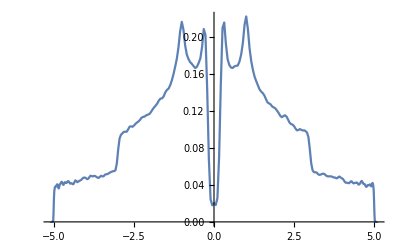

```mathematica
ListLinePlot[DOSKPM[sysΔ[0.1], RandomSamples->4,Rescale->5.1, Order->300]]
```

### Periodic systems

#### Quasi-1D system

A px+ipy superconducting nanoribbon

```mathematica
ribbonregion=Function[{r},0<=r[[1]]≤10];
lat = BuildLattice["Square", Bounded->{Axes->{1},Region->ribbonregion}]
k[r1_,r2_]=-ⅈ (r1-r2)/Norm[r1-r2]^2;
With[{t=1, μ=0.5, Δ=0.5},
pwavehopping=Function[{r1,r2},({{-t, 0}, {0, t}})+Δ({{0, k[r1,r2].{1,-ⅈ}}, {k[r1,r2].{1,ⅈ}, 0}})];
sys=BuildSystem[lat,HoppingRange->1,Onsite->Function[{r},({{-μ, 0}, {0, μ}})],Hopping->pwavehopping]];
```

MQLattice[<NumberOfSites=11, LatticeDimensions=1, EmbeddingDimensions=2>]

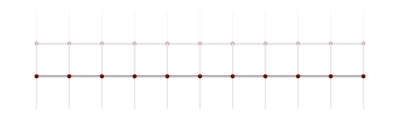

```mathematica
PlotLattice[sys, BoxedCells->False]
```

We want to obtain the bandstructure of this periodic system using Bloch’s theorem: 
	Eigenstates of wavenumber k can be obtained by diagonalising H(k)=H_0+∑_j ⅇ^(ⅈ k·A_j)V_j, where H_0 is the intra-cell and V_j the inter-cell Hamiltonians

To build the k Bloch harmonic of a periodic system sys, use sys[ϕ_1,ϕ_2,...] or sys[{ϕ_1,ϕ_2,...}], where ϕ_j=k·A_j. The full Brillouin zone is spanned by ϕ_j∈[0,2π)

```mathematica
sys
sys[ϕ]
```

MQSystem[<NumberOfSites=11, SiteDimensions=2, LatticeDimensions=1>]

MQSystem[<NumberOfSites=11, SiteDimensions=2, LatticeDimensions=0>]

```mathematica
MatrixForm[sys["H"]]
MatrixForm[sys[ϕ]["H"]]
```

((-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5 | 0
0 | 0.5))

((-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)) | (-1. | 0.-0.5 ⅈ
0.-0.5 ⅈ | 1.)
(0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (0 | 0
0 | 0) | (-1. | 0.+0.5 ⅈ
0.+0.5 ⅈ | 1.) | (-0.5-1. ⅇ^(-ⅈ ϕ)-1. ⅇ^(ⅈ ϕ) | (-0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)+(0.5+0. ⅈ) ⅇ^(ⅈ ϕ)
(0.5+0. ⅈ) ⅇ^(-ⅈ ϕ)-(0.5+0. ⅈ) ⅇ^(ⅈ ϕ) | 0.5+1. ⅇ^(-ⅈ ϕ)+1. ⅇ^(ⅈ ϕ)))

This is manual way to obtain the bandstructure of the nanoribbon

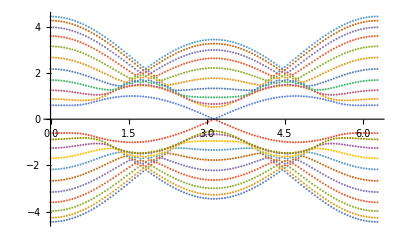

```mathematica
bands=Table[Spectrum[sys[ϕ]],{ϕ,0,2π,2π/120}];
ListPlot[Transpose[bands], DataRange->{0,2π}]
```

Given how often one needs to do this, we have two custom commands

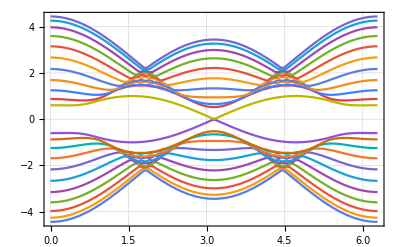

```mathematica
bands=Bands[sys[ϕ],{ϕ,0,2π}, SamplePoints->120];
PlotBands[bands]
```

An more sophisticated UntangledBands algorithm can be used to connect adjacent eigenvalues correctly (using eigenstates)

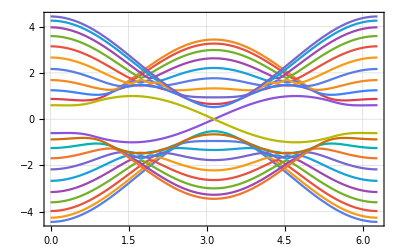

```mathematica
bands=UntangledBands[sys[ϕ],{ϕ,0,2π},SamplePoints->120];
PlotBands[bands]
```

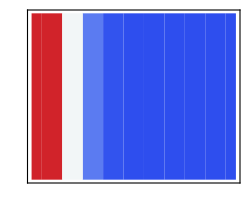
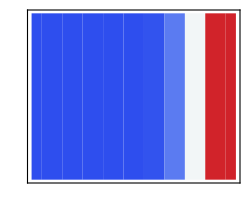

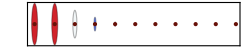
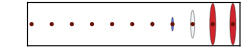

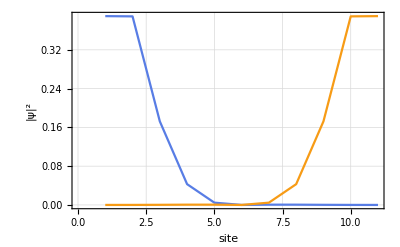

```mathematica
PlotEigenstates[sys[1.01π],Levels->2]
PlotEigenstates[sys[1.01π],Levels->2, BubblePlot->True, Overlay->True]
ListLinePlot[
Eigenstates[sys[1.01π],Levels->2, OrbitalFunction->Function[{ψ},Norm[ψ]^2]],
FrameLabel->{"site","|ψ|^2"},PlotDefaults]
```

#### 2D system

2D chiral superconductor

```mathematica
ribbonregion=Function[{r},0<=r[[1]]≤10];
lat = BuildLattice["Square"]
k[r1_,r2_]=-ⅈ (r1-r2)/Norm[r1-r2]^2;
With[{t=1, μ=0.5, Δ=0.5},
pwavehopping=Function[{r1,r2},({{-t, 0}, {0, t}})+Δ({{0, k[r1,r2].{1,-ⅈ}}, {k[r1,r2].{1,ⅈ}, 0}})];
sys=BuildSystem[lat,HoppingRange->1,Onsite->Function[{r},({{-μ, 0}, {0, μ}})],Hopping->pwavehopping]];
```

MQLattice[<NumberOfSites=1, LatticeDimensions=2, EmbeddingDimensions=2>]

```mathematica
bands=Bands[sys[ϕ1, ϕ2],{ϕ1,0,2π},{ϕ2,0,2π}];
PlotBands[bands, AxesLabel->{"ϕ_1","ϕ_2","energy"}]
```

-Graphics3D-

Graphene

```mathematica
sys=BuildSystem[BuildLattice["Honeycomb"],HoppingRange->1/√3]
PlotBands[Bands[sys[{kx,ky}.({{Cos[π/3], -Cos[π/3]}, {Sin[π/3], Sin[π/3]}})],{kx,-(4π)/3,(4π)/3},{ky,-(2π)/(√3),(2π)/(√3)}],AxesLabel->{"k_x","k_y","energy"}]
```

MQSystem[<NumberOfSites=2, SiteDimensions=1, LatticeDimensions=2>]

-Graphics3D-

The Brillouin zone extends periodically beyond the first

```mathematica
PlotBands[Bands[sys[{kx,ky}.({{Cos[π/3], -Cos[π/3]}, {Sin[π/3], Sin[π/3]}})],{kx,-3(4π)/3,3(4π)/3},{ky,-3(2π)/(√3),3(2π)/(√3)}],AxesLabel->{"k_x","k_y","energy"},
MeshFunctions->{Function[{x,y,z},y]}, Mesh->1]
```

-Graphics3D-

A 1D cut of the above at k_y=0

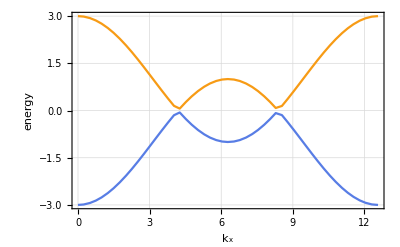

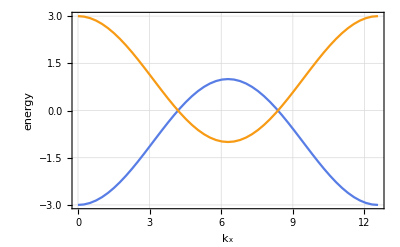

```mathematica
PlotBands[Bands[sys[{kx,0}.({{Cos[π/3], -Cos[π/3]}, {Sin[π/3], Sin[π/3]}})],{kx,0,4π}], FrameLabel->{"k_x","energy"}]
PlotBands[UntangledBands[sys[{kx,0}.({{Cos[π/3], -Cos[π/3]}, {Sin[π/3], Sin[π/3]}})],{kx,0,4π}],FrameLabel->{"k_x","energy"}]
```

If we want to “wrap” one dimension only, use the keyword None for the dimension that should remain open

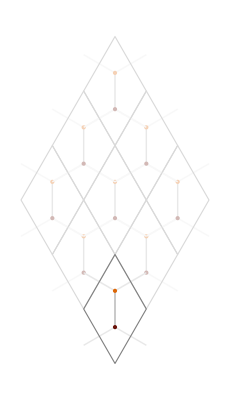

```mathematica
PlotLattice[sys, UnitCells->3]
```

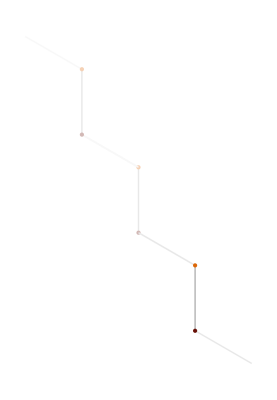

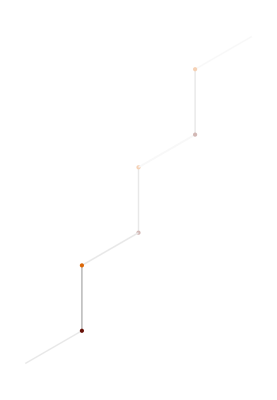

```mathematica
PlotLattice[sys[ϕ, None],UnitCells->3,BoxedCells->False]
PlotLattice[sys[None,ϕ],UnitCells->3,BoxedCells->False]
```

Missing Bloch phases are interpreted as trailing None’s

```mathematica
sys[ϕ]==sys[ϕ,None]
```

True

## Lesson 4 - Building a ScatteringSystem

A transport system consists of N semi-infinite periodic leads, attached to a central system.

```mathematica
lead1=BuildLattice["Honeycomb",Tags->{"1"},Bounded->{Axes->{1},Region->Function[{r},Abs[r[[1]]]<2]}]
lead2=BuildLattice["Honeycomb",Tags->{"2"},Bounded->{Axes->{2},Region->Function[{r},Abs[r[[1]]]<3]}]

central = BuildLattice["Triangular",Tags->{"C"},Bounded->{Axes->All,Region->Function[{r},Norm[r]<9]}]
```

MQLattice[<NumberOfSites=14, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=22, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=297, LatticeDimensions=0, EmbeddingDimensions=2>]

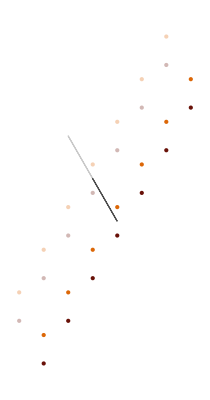
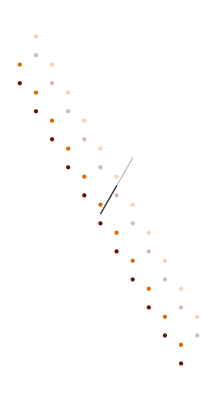
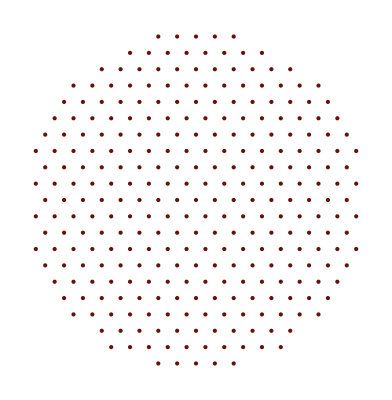

```mathematica
{PlotLattice[lead1],PlotLattice[lead2],PlotLattice[central]}
```

To attach the leads to the central region, we need to reshape their unit cell to the shape of the central region (its complementary).

```mathematica
lead1=BuildLattice[lead1, Reshape->{Region->Function[{r},Norm[r]>9]}]
lead2=BuildLattice[lead2, Reshape->{Region->Function[{r},Norm[r]>9]}]
```

MQLattice[<NumberOfSites=14, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=22, LatticeDimensions=1, EmbeddingDimensions=2>]

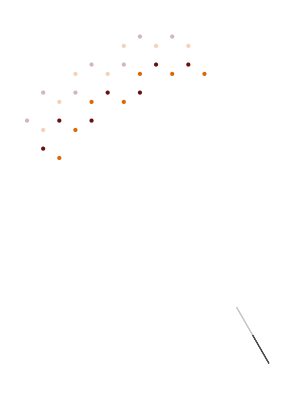

```mathematica
PlotLattice[lead1]
```

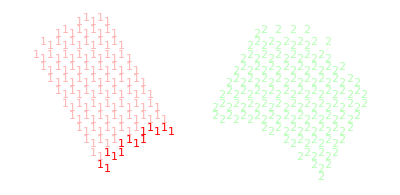

```mathematica
PlotLattice[{lead1,lead2,central}, UnitCells->10, BoxedCells->False, SiteColors->{{Red},{Green},{Blue}}, Labels->"Tags"]
```

The scattering system is built just like a regular system, but using BuildScatteringSystem[central, {lead1,lead2,...}, opts...]
A useful option is CouplingFactor, which multiplies the hoppings between leads and central region by a constact factor.

```mathematica
scatsys=BuildScatteringSystem[central,{lead1,lead2},HoppingRange->1,
Hopping->Function[{r1,r2,tag1,tag2},If[tag1==tag2,If[tag1=="C",1,If[Norm[r1-r2]>1/√3,0,1]],1]],
CouplingFactor->0.5]
```

MQScatteringSystem[<NumberOfLeads=2, CentralSites=297, LeadSites={14, 22}, Nambu=False>]

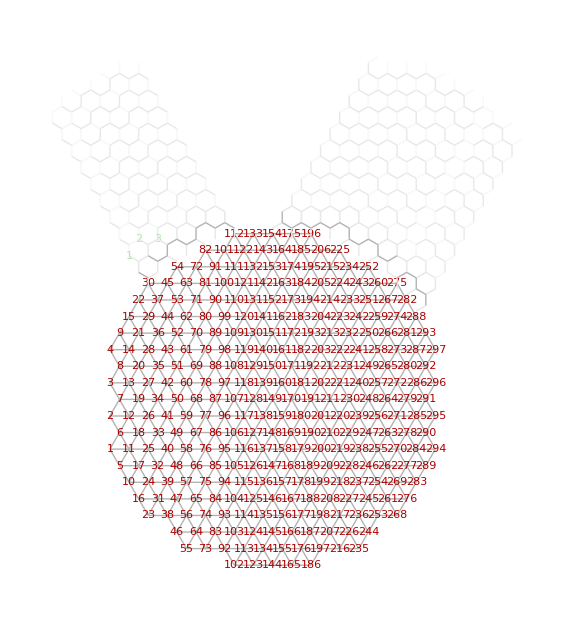

```mathematica
PlotLattice[scatsys,UnitCells->10, BoxedCells->False, SiteColors->{{Darker[Red]},{Darker[Green]},{Darker[Blue]}}, Labels->"Numbers"]
```

```mathematica
scatsys["Central"]
scatsys["Leads"]
scatsys["Couplings"]
scatsys["Nambu"]
```

MQSystem[<NumberOfSites=297, SiteDimensions=1, LatticeDimensions=0>]

{MQSystem[<NumberOfSites=14, SiteDimensions=1, LatticeDimensions=1>],MQSystem[<NumberOfSites=22, SiteDimensions=1, LatticeDimensions=1>]}

{MQSystem[<NumberOfSites=14, SiteDimensions=1, LatticeDimensions=0>],MQSystem[<NumberOfSites=22, SiteDimensions=1, LatticeDimensions=0>]}

False

## Lesson 5 - Computing transport

### Normal systems

Let us rebuild our sample scattering system with a magnetic flux in the central region (Peierls phase in the hoppings)

```mathematica
lead1=BuildLattice["Honeycomb",Tags->{"1"},Bounded->{Axes->{1},Region->Function[{r},Abs[r[[1]]]<2]},Reshape->{Region->Function[{r},Norm[r]>9]}]
lead2=BuildLattice["Honeycomb",Tags->{"2"},Bounded->{Axes->{2},Region->Function[{r},Abs[r[[1]]]<3]},Reshape->{Region->Function[{r},Norm[r]>9]}]
central = BuildLattice["Triangular",Tags->{"C"},Bounded->{Axes->All,Region->Function[{r},Norm[r]<9]}]
```

MQLattice[<NumberOfSites=14, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=22, LatticeDimensions=1, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=297, LatticeDimensions=0, EmbeddingDimensions=2>]

```mathematica
With[{A=Function[{r},{0.,r[[1]]}]},
scatsysB[B_]=BuildScatteringSystem[central,{lead1,lead2},HoppingRange->1,
Hopping->Function[{r1,r2,tag1,tag2},If[tag1==tag2,If[tag1=="C",ⅇ^(ⅈ B A[(r1+r2)/2].(r1-r2)),If[Norm[r1-r2]>1/√3,0,1]],1]]]]
```

MQScatteringSystem[<NumberOfLeads=2, CentralSites=297, LeadSites={14, 22}, Nambu=False>]

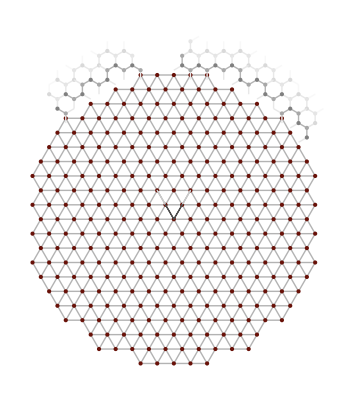

```mathematica
PlotLattice[scatsysB[0]]
```

We may compute the bandstructure of the leads

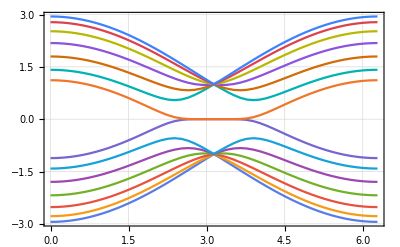

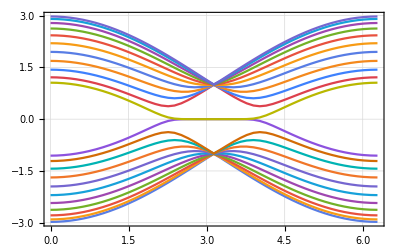

```mathematica
PlotBands[Bands[scatsysB[0]["Leads"][[1]][ϕ],{ϕ,0,2π}]]
PlotBands[Bands[scatsysB[0]["Leads"][[2]][ϕ],{ϕ,0,2π}]]
```

We compute the conductance as a function of Fermi energy at zero flux.

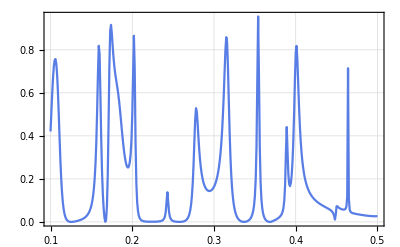

```mathematica
Table[{ϵF,Conductance[ϵF, scatsysB[0]]},{ϵF, 0.1,0.5,0.001}];
ListLinePlot[%, PlotDefaults]
```

Sampling can also be done using Sample. We do a finite flux.

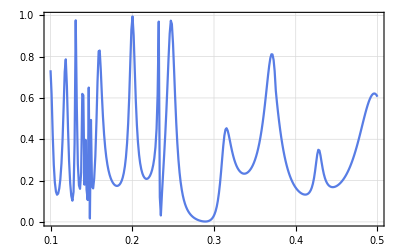

```mathematica
Sample[Conductance[ϵF, scatsysB[.8]],{ϵF,0.1,0.5}, SamplePoints->300];
ListLinePlot[%, PlotDefaults]
```

We can compute the full scattering matrix, S(ω)=(t_11 | t_12
t_21 | t_22.1c). Each t_ij submatrix has a dimension equal to the number of propagating modes at a given energy ω in lead i and j.

```mathematica
Smatrix[0.4,scatsysB[.8]]
MatrixForm@Map[MatrixForm,%,{2}]
```

{{{{0.0354762+0.912846 ⅈ}},{{-0.0379704+0.132801 ⅈ,-0.171975-0.057939 ⅈ,-0.167764-0.29206 ⅈ}}},{{{-0.294504-0.0629008 ⅈ},{0.00318126-0.0293499 ⅈ},{0.241288-0.125192 ⅈ}},{{0.0905277-0.110648 ⅈ,-0.724429+0.115882 ⅈ,-0.45974+0.37321 ⅈ},{-0.88999-0.0379136 ⅈ,0.198186-0.0368335 ⅈ,-0.387875+0.120529 ⅈ},{-0.408611-0.00106094 ⅈ,-0.622943-0.0122194 ⅈ,0.552062-0.257223 ⅈ}}}}

((0.0354762+0.912846 ⅈ) | (-0.0379704+0.132801 ⅈ | -0.171975-0.057939 ⅈ | -0.167764-0.29206 ⅈ)
(-0.294504-0.0629008 ⅈ
0.00318126-0.0293499 ⅈ
0.241288-0.125192 ⅈ) | (0.0905277-0.110648 ⅈ | -0.724429+0.115882 ⅈ | -0.45974+0.37321 ⅈ
-0.88999-0.0379136 ⅈ | 0.198186-0.0368335 ⅈ | -0.387875+0.120529 ⅈ
-0.408611-0.00106094 ⅈ | -0.622943-0.0122194 ⅈ | 0.552062-0.257223 ⅈ))

```mathematica
MatrixForm[Smatrix[2,2,0.4,scatsysB[.8]]]
```

(0.0905277-0.110648 ⅈ | -0.724429+0.115882 ⅈ | -0.45974+0.37321 ⅈ
-0.88999-0.0379136 ⅈ | 0.198186-0.0368335 ⅈ | -0.387875+0.120529 ⅈ
-0.408611-0.00106094 ⅈ | -0.622943-0.0122194 ⅈ | 0.552062-0.257223 ⅈ)

We can compute scattering states

```mathematica
ScatteringStates[0.4, scatsysB[0]]
```

MQScatteringStates[<PropModes={1, 3}, NumberOfLeads=2, LeadCells={{1, 1}, {1, 1}}>]

We can plot scattering states incoming from each of the leads at a given energy

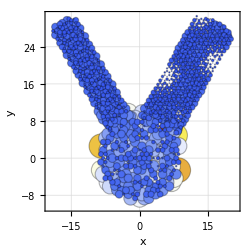

```mathematica
With[{B=0, ϵF=0.4},
PlotScatteringStates[scatsysB[B],
ScatteringStates[ϵF, scatsysB[B],LeadCells->25],
Lead->1,BubblePlot->True]]
```

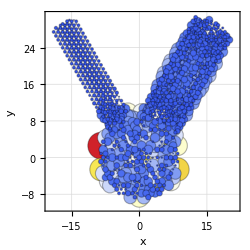
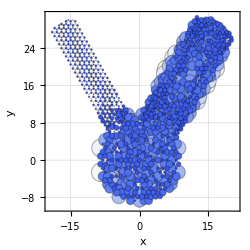
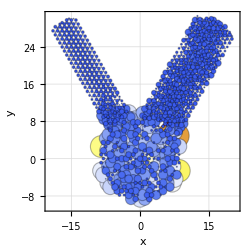

```mathematica
With[{B=0, ϵF=0.4},
PlotScatteringStates[scatsysB[B],
ScatteringStates[ϵF, scatsysB[B],LeadCells->25],
Lead->2,BubblePlot->True]]
```

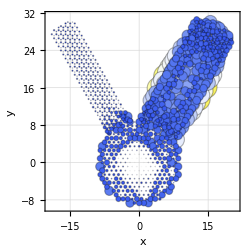
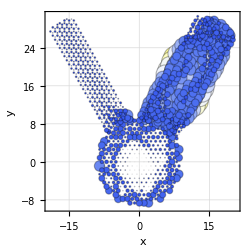
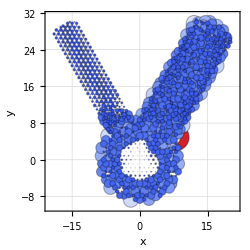

```mathematica
With[{B=0.8, ϵF=0.4},
PlotScatteringStates[scatsysB[B],
ScatteringStates[ϵF, scatsysB[B],LeadCells->25],
Lead->2,BubblePlot->True]]
```

### Superconducting systems

#### NS systems

We can build a normal lead coupled to a (grounded) superconducting island

```mathematica
central = BuildLattice["Square",Tags->"S",Bounded->{Axes->All,Region->Function[{r},Abs[r[[1]]]<6 &&Abs[r[[2]]]<6]}]
lead=BuildLattice["Square",Tags->"N",Supercell->-1,Bounded->{Axes->{2},Region->Function[{r},Abs[r[[2]]]<3]},
Reshape->{Region->Function[{r},r[[1]]≤-6]}]

With[{μ=0.2, Δ=0.5, t=0.1},
scatsys=BuildScatteringSystem[central,{lead},
Onsite->Function[{r,tag},If[tag=="N",({{-μ, 0}, {0, μ}}),({{-μ, Δ}, {Δ, μ}})]],
Hopping->Function[{r1, r2},({{-t, 0}, {0, t}})],
Nambu->True]
]
```

MQLattice[<NumberOfSites=121, LatticeDimensions=0, EmbeddingDimensions=2>]

MQLattice[<NumberOfSites=5, LatticeDimensions=1, EmbeddingDimensions=2>]

MQScatteringSystem[<NumberOfLeads=1, CentralSites=121, LeadSites={5}, Nambu=True>]

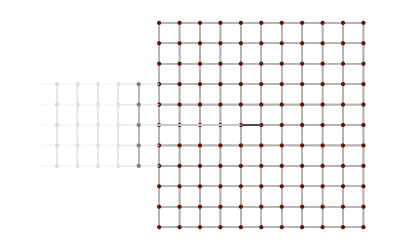

```mathematica
PlotLattice[scatsys, UnitCells->5, SiteTooltips->True]
```

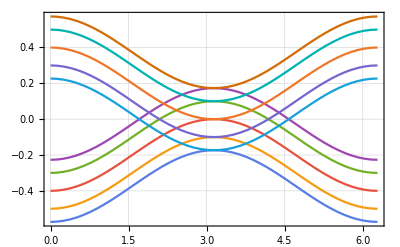

```mathematica
PlotBands[UntangledBands[scatsys["Leads"][[1]][ϕ],{ϕ,0,2π}]]
```

While the system has zero normal conductance, there is a finite BTK conductance. The Nambu->True option indicates that BTK should be used

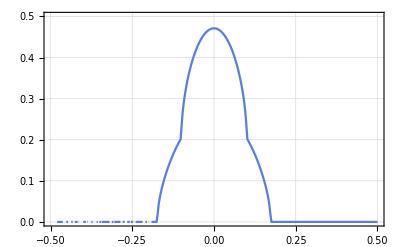

```mathematica
Sample[Conductance[1,ϵF,scatsys],{ϵF,-0.5,0.5}, SamplePoints->300];
ListLinePlot[%,PlotRange->{0,0.5},PlotDefaults]
```

MQScatteringStates[<PropModes={5}, NumberOfLeads=1, LeadCells={{20}}>]

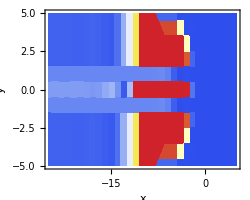
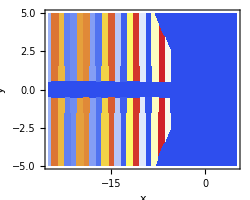
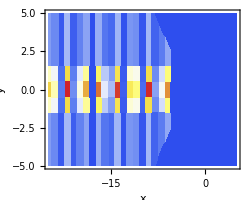
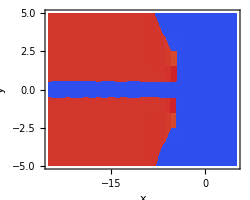
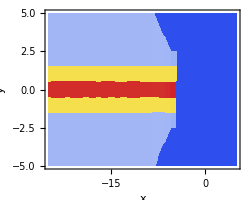

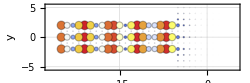
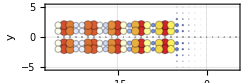
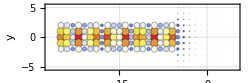

```mathematica
states=ScatteringStates[0.045, scatsys, LeadCells->20]
PlotScatteringStates[scatsys,states,PlotFunction->Function[{ψ},Abs[ψ[[1]]]^2],PlotLegends->False]
PlotScatteringStates[scatsys,states,PlotFunction->Norm,BubblePlot->True]
```

## Lesson 6 - Advanced topics [Work in progress]

Supercurrents

```mathematica
BuildLattice["Linear",Bounded->{Region->(Abs[#[[1]]]<100&)}]
```

MQLattice[<NumberOfSites=199, LatticeDimensions=0, EmbeddingDimensions=1>]

```mathematica
With[{Δ=0.2, t=1, μ=0.2},
sysϕ[ϕ_, B_]=BuildSystem[BuildLattice["Linear",Bounded->{Region->(Abs[#[[1]]]<100&)}],Onsite->(({{-μ, B, 0, Δ ⅇ^(-ⅈ ϕ Sign[#[[1]]]/2)}, {B, -μ, -Δ ⅇ^(-ⅈ ϕ Sign[#[[1]]]/2), 0}, {0, -Δ ⅇ^(ⅈ ϕ Sign[#[[1]]]/2), μ, -B}, {Δ ⅇ^(ⅈ ϕ Sign[#[[1]]]/2), 0, -B, μ}})&), Hopping->(-t({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}})&), Nambu->True]]
```

MQSystem[<NumberOfSites=199, SiteDimensions=4, LatticeDimensions=0>]

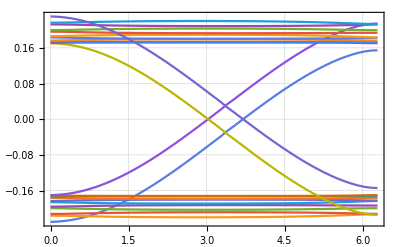

```mathematica
PlotBands[UntangledBands[sysϕ[ϕ, 0.03],{ϕ,0,2π}, Levels->22]]
```

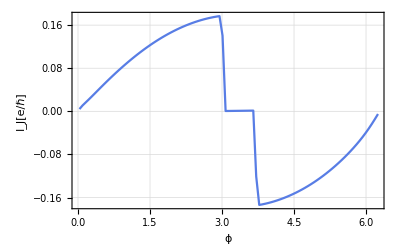

0.176713

```mathematica
JosephsonCurrent[sysϕ[ϕ,0.03],ϕ, Levels->22, SamplePoints->100];
ListLinePlot[%,PlotDefaults, FrameLabel->{"ϕ", "I_J[e/ℏ]"}]
Max[%%[[All,2]]]
```

Elastic Relaxation: SpringMesh, ElasticEnergy, ElasticForces, RelaxLattice, GradientMesh, RelaxField

Band topology: MomentumCycles, BerryCurvature, BerryMesh, ChernNumber

Linear Response: LinearResponseIm, OpticalConductivity, LocalDensityOfStates